# Fortran Flow Reader

fortran flow in this case refers to flux_calc.f, developed by Kolar & Dresback. this code is hardcoded for the EC grid, with the following cross-sections:

tar at greenville (12 nodes)
tar at pamlico (8 nodes)
tar at tarboro (11 nodes)
tar r. 5 nodes into domain (12 nodes)
tar r. 10 nodes into domain (14 nodes)
fishing ck 5 nodes into domain (13 nodes)
fishing ck 10 nodes into domain (14 nodes)

this script reads the output from that program and reports a {time,flow} scatter at each cross section

that file’s format looks like this:

{header info}
{header info}
	for L=1, timesteps
		{time	timestep}
		for i=1, nsegs
			for J=1,nodes in segment -1 (number of element faces in segment)
			{flux}
			end for
		{segmentnumber	avg_depth	avg_V	    segment_Q}
		end for
	end for
~end of file~

whereas the output file format we want looks like this:
{header info},
for i=1, nsegs
{
	for L=1, timesteps
		{absolute time, flow},
	end for
},
end for

```mathematica
(*put "no file" if the flux file doesn't exist*)
segmentlengths={12,8,11,12,14,13,14,6,6,30,30,64,63};(*number of nodes in each segment*)
nsegs=Length[segmentlengths];
Js=segmentlengths-1; (*number of element faces in each segment*)

nodestringnames={"Tar At Greenville","Tar At Pamlico","Tar At Tarboro","Tar Handoff +5 Nodes","Tar Handoff +10 Nodes","Fishing Handoff +5 Nodes","Fishing Handoff +10 Nodes","Tar Handoff","Fishing Handoff","some bullshit","some bullshit","some bullshit","some bullshit"};
signs={-1,1,-1,1,1,-1,1,1,1,1,1,1,1};
(*..................................................................................Irene.............................
spinupinputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\spinup.flux";
hurricaneinputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\hurricane.flux";
spindowninputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\spindown.flux";
outputfile="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\spinup_hurricane_fluxscatters";
filestarttime="July 06, 2011"//AbsoluteTime;
*)

(*................................................Floyd...............................................................
spinupinputfile="D:\\Dropbox\\Floyd\\river_fluxes\\spinup.txt";
hurricaneinputfile="D:\\Dropbox\\Floyd\\river_fluxes\\hurricane.txt";
spindowninputfile="D:\\Dropbox\\Floyd\\river_fluxes\\spindown.txt";
outputfile="D:\\Dropbox\\Floyd\\river_fluxes\\combined.txt";
filestarttime="Sep 13, 1999"//AbsoluteTime;
rundays=31+6+30;
*)

(*................................................Floyd_norivers...............................................................*)
spinupinputfile="D:\\Dropbox\\floyd_norivers\\spinup_flow.txt";
hurricaneinputfile="D:\\Dropbox\\floyd_norivers\\hurricane_flow.txt";
spindowninputfile="D:\\Dropbox\\floyd_norivers\\spindown_flow.txt";
outputfile="D:\\Dropbox\\floyd_norivers\\adc_flow_combined.csv";
filestarttime="Sep 13, 1999"//AbsoluteTime;
rundays=31+6+30;
nstorms=3;

segmentlengths={18};(*number of nodes in each segment*)
nsegs=Length[segmentlengths];
Js=segmentlengths-1; (*number of element faces in each segment*)

nodestringnames={"Pamlico at Washington"};
signs={-1};



(*................................................April, 2003...............................................................
spinupinputfile="D:\\Dropbox\\april2003\\river results\\river_fluxes.txt"
outputfile="D:\\Dropbox\\april2003\\river results\\combined.txt";
filestarttime="Mar 15, 2003"//AbsoluteTime;
rundays=60;
*)
```

```mathematica
(*step 1- import spinup file*)
inp={spinupinputfile,hurricaneinputfile,spindowninputfile};

Qgrab=Table[0,{3}];
Do[
inputfile=inp[[storm]];





Qgrab[[storm]]=Catch[


If[inputfile=="no file",
Throw["error - no file selected"];
];

in=OpenRead[inputfile];
(*STEP 1 - CHECK FOR COMPLETENESS*)
junk=Read[in,String];
stepsheader=Read[in,Number];
junk=Read[in,String];



(*get filelength*)
entries=ReadList[in,String];(*these are all the individual entries*)
filelength=Length[entries];
(*figure out how many output entries there are in the file*)
(*the file has 2 header lines*)

(*at each timestep, there is one line plus one for each segment node*)
perstep=1+Sum[segmentlengths[[i]],{i,1,Length[segmentlengths]}];
nsteps=filelength/perstep;
If[nsteps≠stepsheader,
Print["error-steps don't match"];
Print[storm]
];

(*now that we know the number of lines in each step (perstep) we can import all the data*) 
Close[in];






in=OpenRead[inputfile];

outputlist={"header",Table[0,{nsegs}]};

header=Read[in,String];
junk=Read[in,String];
raw=ReadList[in,Word];
Close[in]
(*clean the entries*)
Do[
If[raw[[i]]=="NaN",
raw[[i]]=-9999,
raw[[i]]=StringReplace[raw[[i]],{"E+"->"*^","E-"->"*^-"}];
raw[[i]]=raw[[i]]//ToExpression]
,{i,1,Length[raw]}];



(*step 1 - partition raw into each timestep entry.*)
(*the quick way to do this is to use nsteps and filelength to get the entries per step.*)
(*note that we can't just use the prior value of "perstep" because at this point, *)
(* "perstep" is in lines, and we need it in numbers*)
(*e.g. each timestep line is one line, 2 numbers, etc*)
perstep=Length[raw]/nsteps;
raw=Partition[raw,perstep];
raw=Transpose[raw];
(*now raw is a bunch of vectorized entries with the following form*)
(*
time
timestep
(for i = 1 -> nsegs)
node i,1
node i,2
node i,3
....
node i,J(i)
segmentnumber(i)
avg_depth(i)
avg_V(i)
segment_Q(i)
*)


(*from that vectorization, it becomes clear that the index of each segment_Q(i) is as follows:
2 (time+timestep)
plus the number of nodes of each preceeding segment, including the one itself
+Sum(J(i'), i' 1->i)
plus three for each preceeding segment, including the one itself
+3*i
plus one for each preceeding segment_Q
+(i-1)
*)
Qindices=Table[2
+Sum[Js[[i2]],{i2,1,i}]
+3*i
+(i)
,{i,1,nsegs}];


times=raw[[1]];
times=times+filestarttime;
endtime=times[[Length[times]]];

Qseries=Table[{times,signs[[i]]*raw[[Qindices[[i]]]]}//Transpose,{i,1,Length[Qindices]}];
Throw[Qseries];



]

,{storm,1,3}];
```

```mathematica
GraphicsGrid[
Partition[
Table[
Show[
scatterplot[Qgrab[[2,i]],filestarttime,filestarttime+rundays*24*60*60,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Blue],
scatterplot[Qgrab[[1,i]],filestarttime,filestarttime+rundays*24*60*60,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Red],
scatterplot[Qgrab[[3,i]],filestarttime,filestarttime+rundays*24*60*60,0,1800,"Q - CMS","Date",nodestringnames[[i]],7,True,Green]
]
,{i,Length[Qgrab[[2]]]}]
,3]
]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

GraphicsGrid::list: {} is not a list of lists.

GraphicsGrid[{}]

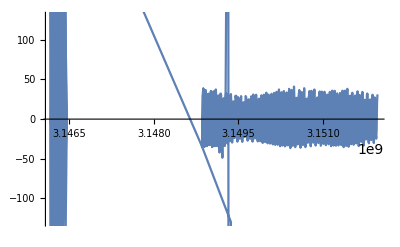

```mathematica
ListPlot[Partition[Flatten[Qgrab],2],Joined->True]
```

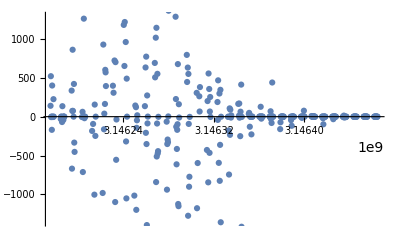

```mathematica
ListPlot[Qgrab[[1,1]]]
```